```mathematica
SetDirectory["/Volumes/192.168.1.39/stran/data"]
```

/Volumes/192.168.1.39/stran/data

```mathematica
FileNames["*.csv"]
```

{bmp085-p.csv,delta-p.csv,delta-t.csv,DP.csv,hh10d.csv,HI.csv,load.csv,napoved-dp.csv,napoved-h.csv,napoved-hi.csv,napoved-p.csv,napoved-t.csv,stat-dp.csv,stat-h.csv,stat-p.csv,stat-t.csv,temp.csv,zambretti.csv,zdej-dp.csv,zdej-h.csv,zdej-hi.csv,zdej-p.csv,zdej-t.csv}

```mathematica
imp=Rest[Import["temp.csv","Data"]]
```

{{2012/07/12 17:22:00,30.6,},{2012/07/12 17:27:01,30.8,},{2012/07/12 17:32:01,30.8,},{2012/07/12 17:33:02,30.9,},{2012/07/12 17:54:01,30.9,},«23917»,{2012/09/16 01:47:02,24.2,24.8},{2012/09/16 01:55:04,24.2,24.8},{2012/09/16 01:56:02,24.2,24.7},{2012/09/16 01:57:01,24.1,24.7}}

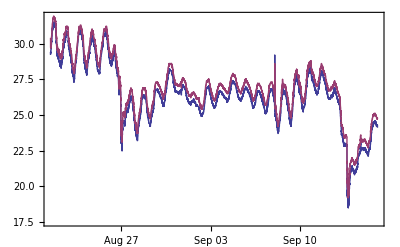

```mathematica
DateListPlot[{imp⟦13050;;-1,{1,2}⟧,imp⟦13050;;-1,{1,3}⟧},Joined->True]
```

```mathematica
data=Sort[Select[imp⟦13050;;-1,{2,3}⟧,#⟦1⟧≠""∧#⟦2⟧≠""&]];
```

```mathematica
fit=LinearModelFit[data,x,x];
Normal[fit]
```

1.11994+0.97737 x

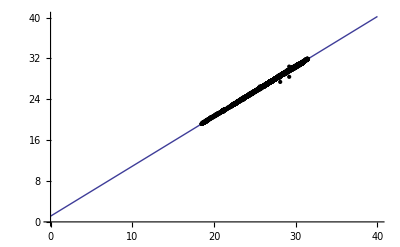

```mathematica
Plot[fit[x],{x,0,40},Epilog->Point/@data]
```